```mathematica
teoricos = Import["teorico.csv", "Dataset", "HeaderLines"->1];
```

```mathematica
ejec1 = Import["C:\\Users\\pdbru\\Desktop\\tesis\\ADC-pauli-quantum-QPU-optimized-EM.csv", "Dataset", "HeaderLines"->1];
ejec2 = Import["C:\\Users\\pdbru\\Desktop\\tesis\\ADC-pauli-quantum-QPU-optimized-EM-2.csv", "Dataset", "HeaderLines"->1];
ejecOptim = Import["C:\\Users\\pdbru\\Desktop\\tesis\\ADC-pauli-quantum-QPU-optimized-EM-optim3.csv", "Dataset", "HeaderLines"->1];
```

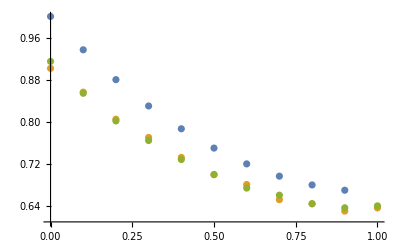

```mathematica
ps = {0, 0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8, 0.9, 1};puntosParaDataset[ds_] := Table[{p, ds[Select[(#chA == "ADC" && #chB == "ADC" && #d =="fidelity" && #pA ==p && #pB ==p)&], "score"][1]}, {p, ps}];
ListPlot[{puntosParaDataset[teoricos], puntosParaDataset[ejec2], puntosParaDataset[ejecOptim]}]
```